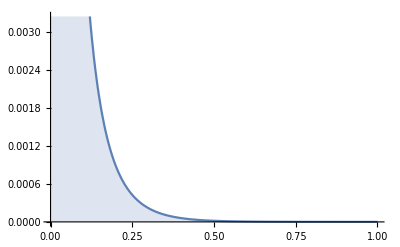

```mathematica
a = 0.0012960000000000003;
Plot[PDF[GammaDistribution[a,0.1],x]//Evaluate,{x,0,10^(0)},Filling->Axis]
```

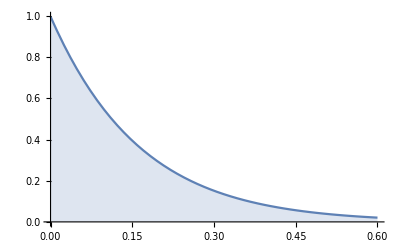

```mathematica
Plot[PDF[PoissonDistribution[a],x]//Evaluate,{x,0,0.6},Filling->Axis]
```

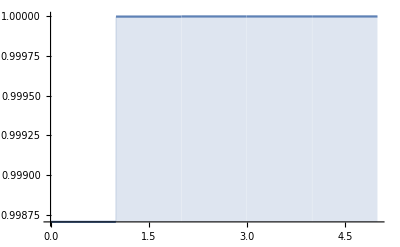

```mathematica
Plot[CDF[PoissonDistribution[a],x]//Evaluate,{x,0,5},Filling->Axis]
```

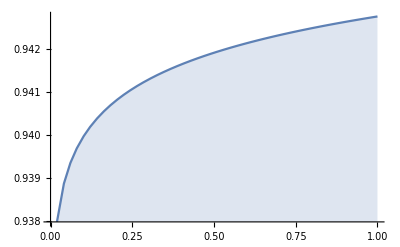

```mathematica
Plot[CDF[GammaDistribution[a,1],x]//Evaluate,{x,0,10^(-20)},Filling->Axis]
```

```mathematica
Plot[CDF[PoissonDistribution[a],x]//Evaluate,{x,0,100},Filling->Axis]
```

-Graphics-

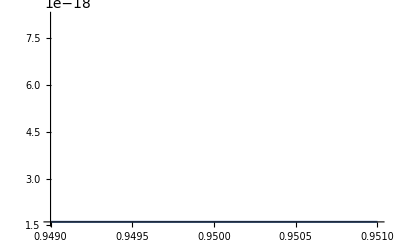

```mathematica
(*a = 0.00025920000000000007;*)
Plot[InverseCDF[GammaDistribution[0.001296,1],x]//Evaluate,{x,0.949,0.951},Filling->Axis]
```

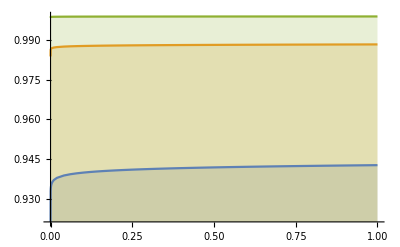

```mathematica
Plot[Table[CDF[GammaDistribution[a,1],x],{a,{0.001296,0.0002592,0.00002592}}]//Evaluate,{x,0,10^(-20)},Filling->Axis]
```